## Eli’s Wolfram Language Cheat Sheet

```mathematica
(*@ puts brackets around a thing*)
f@{g,h,i}
```

f[{g,h,i}]

```mathematica
(*it is useful for functions that only require one input*)
```



```mathematica
Graphics@Disk[]
```

```mathematica
Sqrt@4
```

2

```mathematica
IntegerQ@10
```

True

```mathematica
(*@@ replaces list brackets and inserts the whole list directly into the function*)
f@@{g,h,i}
```

f[g,h,i]

```mathematica
(*this works for functions that take more than one argument*)
```

```mathematica
NestList@@{#^2&,2,2}
```

{2,4,16}

```mathematica
Table@@{x+y,{x,10},{y,10}}
```

{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}

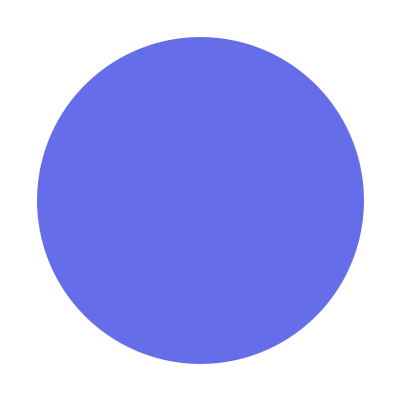

```mathematica
Graphics[Style@@{Disk[],RandomColor[]}]
```

```mathematica
(*@@@ operates on lists within a list*)
```

```mathematica
f@@@{{g},{h},{i}}
```

{f[g],f[h],f[i]}

```mathematica
Plus@@@{{1,2},{3,4}}
```

{3,7}

```mathematica
FromLetterNumber@@{{2},{3}}
```

FromLetterNumber[{2},{3}]

```mathematica
FromLetterNumber@@@{{2},{3}}
```

{b,c}

```mathematica
(*/@ does the same thing as @@@*)
```

```mathematica
f/@{g,h,i}
```

{f[g],f[h],f[i]}

```mathematica
(*except /@ also works with pure functions*)
```

```mathematica
#^2&/@{1,2,3}
```

{1,4,9}

```mathematica
(*@@@ does not work with pure functions*)
```

```mathematica
#^2&@@@{1,2,3}
```

{1,2,3}

```mathematica
(*module is pretty simple. you set a condition and then evaluate an equation with that condition*)
```

```mathematica
Module[{x=2},3x+5x+7]
```

23

```mathematica
(*Module is functionally the same *)
```

```mathematica
(*Array works with a list of lists of the same size*)
```

```mathematica
Array[f,9,2]
```

{f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
(*You know how to do table*)
```

```mathematica
Table[x+y,{x,3},{y,3}]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
(*/. replaces things from a list*)
```

```mathematica
{a,b,c}/.c->d
```

{a,b,d}

```mathematica
(*an array is a list of lists*)
```

```mathematica
ArrayQ[{1,2},{3,4},{5,6}]
```

False

```mathematica
ArrayQ[{{1,2},{3,4},{5,6}}]
```

True

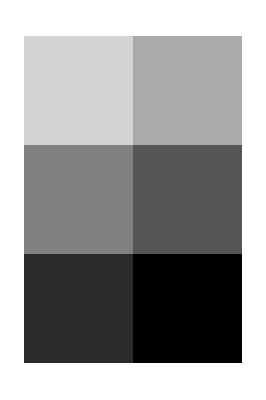

```mathematica
ArrayPlot[{{1,2},{3,4},{5,6}}]
```

```mathematica
(*You can get to an array by partitioning a list*)
```

```mathematica
ArrayQ[Partition[{1,2,3,4},2,1]]
```

True

```mathematica
(*You can group stuff from arrays with transpose]*)
```

```mathematica
Transpose[{{1,2},{3,4},{5,6}}]
```

{{1,3,5},{2,4,6}}

```mathematica
(*You can also pull all of the first, second, etc. variables out of arrays*)
```

```mathematica
{{1,2},{3,4},{5,6}}[[All,1]]
```

{1,3,5}

```mathematica
{{a,b},{c,d},{e,f}}[[2,2]]
```

d